```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
dbg=False;
hbar=197.327053;
Mm=938.858;
m1=Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 41.4738

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./tmp.dat","Table"];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
VlocTF=Compile[{r,lam,Cc},Block[{},
Cc Exp[-0.25 lam^2 r^2]
]];
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

Wmat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0],{i,1,Npoints}]];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,LECc_,energ_:0.001]:=Module[{locall=l},
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

## statistical analysis of the numerical stability of a_dd predictions

Obtain dimer-dimer scattering length for the core ensemble

```mathematica
lambdaTest=8;
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.01;
(* Integration grid *)
rMa=26;
grdPerFermi=58;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
tmp=GetERE[lambdaTest,rMa,nGrd,LECc,energ];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,tmp}];
Print[nn,")  ",lambdaTest," ",LECc," ",rMa," ",nGrd," ",energ," ",tmp];

Put[results,"results_aDD_"<>ToString[lambdaTest]<>".res"];
```

nn)  8 -1898.7 26 1508 0.01 4.46258

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

λ = 10   C_0(λ) = -2934.2     R_max = 2     #(grid points) = 80                a_aa = 4.19074

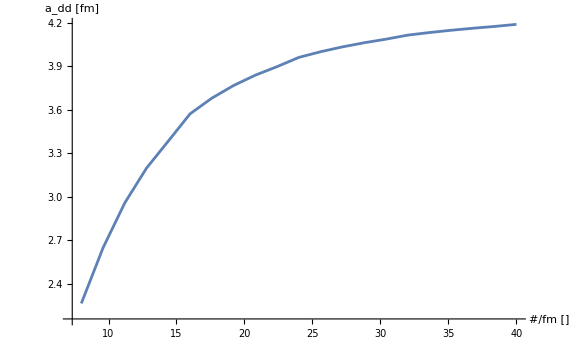

```mathematica
(* regulator cutoff *)
lambdaTest=10;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];

(* energy at which the scattering length is obtained from the amplitude *)
energ=0.01;

(* Integration grid *)
rMaxStart=1;
rMaxEnd=5;
nbrR=20;
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
rMa=2;

pdMaxStart=8;
pdMaxEnd=40;
nbrPD=20;
psmaxRange=Range[pdMaxStart,pdMaxEnd,N[(pdMaxEnd-pdMaxStart)/nbrPD]];
grdPerFermi=25;

results={};

Paras=psmaxRange;
Do[
If[Paras==psmaxRange,grdPerFermi=psmaxRange[[mm]];xLab="#/fm []",rMa=RmaxRange[[mm]];xLab="R_max [fm]"];
nGrd=IntegerPart[rMa grdPerFermi];
tmp=GetERE[lambdaTest,rMa,nGrd,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
,{mm,Length[Paras]}]
Print["λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_aa = ",tmp];
ListPlot[Transpose[{Paras,results}],ImageSize->Large,Joined->True,AxesLabel->{xLab,"a_dd [fm]"}]
```